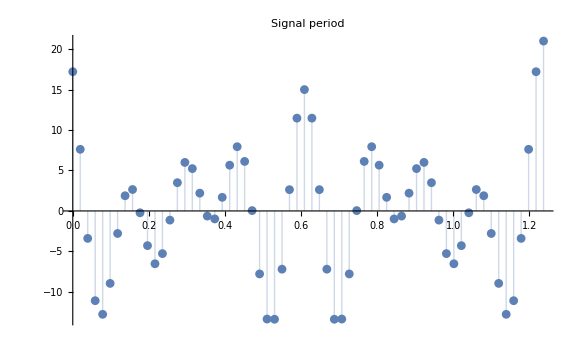

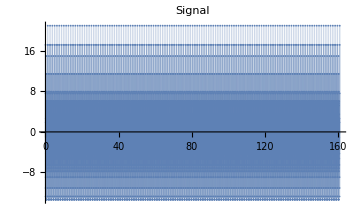

```mathematica
count = 8192;
δt = SetPrecision[0.0196349540849362, 15];

InputList = SetAccuracy[#, 15] & /@ ReadList["C:\\Users\\egorb\\workSpace\\study\\3 курс\\ФОИТ\\ИЗД3\\3.txt", Real]
InputPlot = ListPlot[Table[{ δt*(i - 1), InputList[[i]]}, {i, 64}], Filling -> Axis, ImageSize->Large, PlotLabel->"Signal period"]
FullSignal = ListPlot[Table[{ δt*(i - 1), InputList[[i]]}, {i, count}], Filling -> Axis, PlotLabel->"Signal", ImageSize->Medium]
```

{{-40.0390625,362.0386719675},{-30.0390625,271.529003976},{-20.0390625,181.019335984},{-15.0390625,135.764501988},{15.,135.764501988},{20.,181.019335984},{30.,271.529003976},{40.,362.0386719675}}

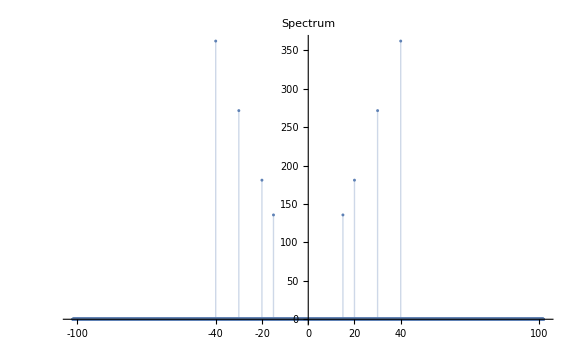

```mathematica
tIN = δt * count;
df = 1 / tIN;

fI[i_] := i * df;
ωI[i_] := 2π(fI[i]);  

ωToI = Floor[count / π];

FI = Fourier[InputList];
Spectrum = Table[{ωI[i - 1], Abs@FI[[i]]}, {i, -ωToI, ωToI}];
neededValues = Select[Spectrum, #[[2]] > 1  &]
ListPlot[Spectrum, Filling -> Axis, PlotLabel->"Spectrum", ImageSize->Large, Ticks->{{-100, -50, -40, -30, -20, -10, 0, 10, 20, 30, 40, 50,  100}, Automatic}]
```

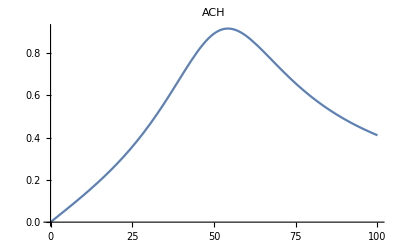

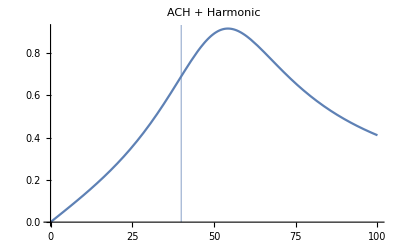

0.690796660681

```mathematica
L1 = SetPrecision[12.8370212487241, 15];
L2 = SetPrecision[0.698772649362423, 15];
C1 = SetPrecision[1.17586224990022 * 10^(-5), 15];
C2 = SetPrecision[1.43766384201593 * 10^(-5), 15];
R1 = SetPrecision[111.409146402624, 15];
R2 = SetPrecision[37.1964110318062, 15];
R3 = SetPrecision[1050.36613674762, 15];
R4 = SetPrecision[538.488361371006, 15];


Z1[ω_]= R4 + 1/(I ω C2);
Z2[ω_]= 1/(I ω C1)+R2 + I ω L2 + R3;
Zparalel[ω_] = 1/(1/Z1[ω]+1/Z2[ω]);
I1[ω_] = Uin/(R1 + I ω L1 + Zparalel[ω]);
Upar[ω_] = I1[ω] * Zparalel[ω];
Ipar2[ω_] = Upar[ω]/Z2[ω];
Uout[ω_] = Ipar2[ω] * R3;
H[ω_]= Uout[ω]/Uin;


harmoniсNumber = 4;
ωMax = 100;

Plot[Abs @ H[ω], {ω, 0, ωMax}, PlotLabel->"ACH"]

Show[
	Plot[Abs @ H[ω], {ω, 0, ωMax}],
	ListPlot[{neededValues[[2 * harmoniсNumber]]}, Filling->Axis], PlotLabel->"ACH + Harmonic"
	]
	
Abs @ H[neededValues[[2 * harmoniсNumber]][[1]]]
```